```mathematica
En=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-01-2006.csv"];
Fe=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-02-2006.csv"];
Mar=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-03-2006.csv"];
Ab=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-04-2006.csv"];
May=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-05-2006.csv"];
Jun=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-06-2006.csv"];
Jul=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-07-2006.csv"];
Ag=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-08-2006.csv"];
Sep=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-09-2006.csv"];
Oc=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-10-2006.csv"];
Nov=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-11-2006.csv"];
Dic=Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos Crudos Públicos  CI01  2006/DP-CI01-12-2006.csv"];
```

```mathematica
y=Join[En,Fe,Mar,Ab,May,Jun,Jul,Ag,Sep,Oc,Nov,Dic]
```

{{1,10,2.45,333.4,0.449,3.488,2.177,0.37,3.104},{1,20,1.878,339.1,0.43,3.106,2.159,0.37,3.104},{1,30,1.403,358.7,0.265,1.96,0.759,0.534,1.953},52554,{365,2340,8.32,29.53,2.133,14.56,10.45,2.3,16.15},{365,2350,7.73,29.61,1.987,15.33,9.5,2.279,16.53},{365,2400,8.29,33.36,2.252,16.47,10.06,2.378,16.91}}
 |  |  |  |

```mathematica
Dimensions[y]
```

{52560,9}

```mathematica
Vel20=y[[All,{2,3}]];
Vel40=y[[All,{2,7}]];
dir=y[[All,{3,4}]];
dir40=y[[All,{7,4}]];
raf20=y[[All,{2,6}]];
raf40=y[[All,{2,9}]];
```

```mathematica
tiempo1=Table[i,{i,10,5760,10}];
```

```mathematica
Vel201=y[[1;;576,{2,3}]];
Vel401=y[[1;;576,{2,7}]];
Vel201[[All,1]]=tiempo1;
Vel401[[All,1]]=tiempo1;
```

```mathematica
Export["Vel20.dat",Vel201]
Export["Vel40.dat",Vel401]
```

Vel20.dat

Vel40.dat

```mathematica
Max[Vel201[[All,2]]]
```

10.12

```mathematica
Max[Vel401[[All,2]]]
```

12.3

```mathematica
Length[Vel40]
```

52560

```mathematica
(*Haremos una lista que incrementemos de 10 min en 10 min. para que tengamos un dato lineal*)
tiempo=Table[i,{i,10,525600,10}];
```

```mathematica
Vel40[[All,1]]=tiempo;
```

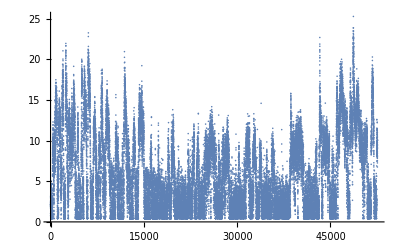

```mathematica
(*El tiempo está desfazado 1/10*)
ListPlot[Vel40[[All,2]]]
```

```mathematica
(*Iteramos para eliminar los valores y guardar la nueva lista en Vel 20 ok y Vel40ok en donde *)
Vel20ok={};  Vel40ok={}; raf20ok={}; raf40ok={};
Do[If[Vel20[[i,2]] ≠0 &&Vel40[[i,2]]≠0 &&raf40[[i,2]]≠0 &&raf40[[i,2]]≠0,
AppendTo[Vel20ok,Vel20[[i]]];AppendTo[Vel40ok,Vel40[[i]]]; AppendTo[raf20ok,raf20[[i]]]; AppendTo[raf40ok,raf40[[i]]];
],{i,1,Length[Vel20]}]
```

```mathematica
(*Datos perdidos*)
Length[raf40]- Length[raf40ok]
```

1524

```mathematica
μr20=Mean[raf20ok[[All,2]]]
σr20=StandardDeviation[raf20ok[[All,2]]]
varianzar20 = Variance[raf20ok[[All,2]]]
modar20=Commonest[raf20ok[[All,2]]]
medianar20=Median[raf20ok[[All,2]]]
minr20 = Min[raf20ok[[All,2]]]
maxr20=Max[raf20ok[[All,2]]]
```

8.51748

6.16959

38.0639

{2.342}

6.924

0.815

36.33

```mathematica
μr40=Mean[raf40ok[[All,2]]]
σr40=StandardDeviation[raf40ok[[All,2]]]
varianzar40 = Variance[raf40ok[[All,2]]]
modar40=Commonest[raf40ok[[All,2]]]
medianar40=Median[raf40ok[[All,2]]]
minr40 = Min[raf40ok[[All,2]]]
maxr40=Max[raf40ok[[All,2]]]
```

9.32246

6.96175

48.4659

{2.721}

7.32

0.419

37.63

```mathematica
μ20=Mean[Vel20ok[[All,2]]]
σ20=StandardDeviation[Vel20ok[[All,2]]]
varianza20 = Variance[Vel20ok[[All,2]]]
moda20=Commonest[Vel20ok[[All,2]]]
mediana20=Median[Vel20ok[[All,2]]]
min20 = Min[Vel20ok[[All,2]]]
max20=Max[Vel20ok[[All,2]]]
```

5.08882

3.79607

14.4102

{7.54}

4.226

0.003

21.02

```mathematica
μ40=Mean[Vel40ok[[All,2]]]
σ40=StandardDeviation[Vel40ok[[All,2]]]
max40=Max[Vel40ok[[All,2]]]
moda40=Commonest[Vel40ok[[All,2]]]
mediana40=Median[Vel40ok[[All,2]]]
max40=Max[Vel40ok[[All,2]]]
min40 = Min[Vel40ok[[All,2]]]
```

6.00374

4.61174

25.29

{0.419}

4.786

25.29

0.419

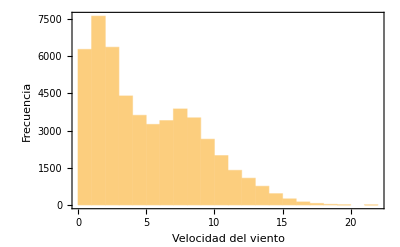

```mathematica
Histogram[Vel20ok[[All,2]],Frame->True,FrameLabel->{"Velocidad del viento","Frecuencia"}]
```

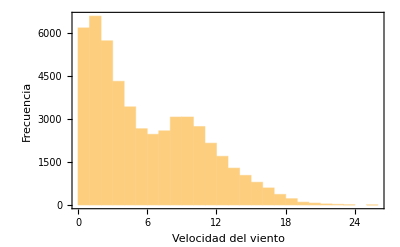

```mathematica
Histogram[Vel40ok[[All,2]],Frame->True,FrameLabel->{"Velocidad del viento","Frecuencia"}]
```

```mathematica
(*Perfil logarítmico*)
uLog[ur_,zr_,z_,z0_]:=ur Log[z/z0]/(Log[zr/z0]);
(*Perfil de potencias*)
z0[u_,ur_,z_,zr_]:=Exp[(u Log[zr]-ur Log[z])/(u-ur)]
```

```mathematica
(*Determinamos la rugosidad del perfil de potencia dando los parámetros como lo marca las variables vref=20 y vel=40*)
Rug=z0[Vel40ok[[All,2]],Vel20ok[[All,2]],40,20];
ListPlot[Rug,PlotRange->{All,{0,10}}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::munfl: Exp[-3145.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2469.46] is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::munfl: Exp[-1555.55] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(*Encontrar la rugosidad promedio*)
```

```mathematica
z0p=Mean@Select[Rug,#<10&]
```

0.993556

```mathematica
(**)
alpha[u_,ur_,z_,zr_]:=Log[u/ur]/Log[z/zr]
```

```mathematica
alfa=alpha[Vel40ok[[All,2]],Vel20ok[[All,2]],40,20];
```

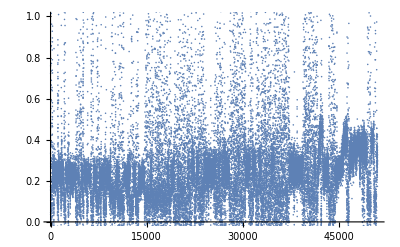

```mathematica
ListPlot[alfa,PlotRange->{All,{0,1}}]
```

```mathematica
(*Coeficiente de cizalladura promedio*)
alfap=Mean@Select[alfa,#<1&]
```

0.160295

```mathematica
PDF[WeibullDistribution[k,c],u]
Mean[WeibullDistribution[k,c]]
```

Piecewise[{{(ⅇ^(-(u/c)^k) k (u/c)^(-1+k))/c, u>0}, {0, True}}]

c Gamma[1+1/k]

```mathematica
(*Aquí solo usamos 1 velocidad*)
FindRoot[{Mean[WeibullDistribution[k,c]]==μ20,StandardDeviation[WeibullDistribution[k,c]]==σ20},{k,2},{c,10}]
```

{k→1.35535,c→5.55338}

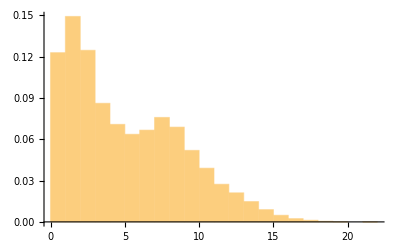

```mathematica
hist=Histogram[Vel20ok[[All,2]],20,"PDF"]
```

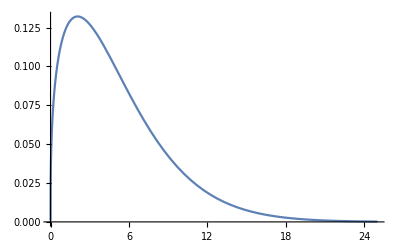

```mathematica
adj=Plot[PDF[WeibullDistribution[1.3553502908129473,5.55337581079599],u],{u,0,25}]
```

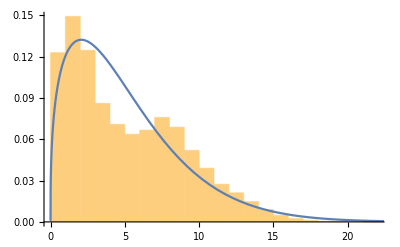

```mathematica
Show[hist,adj]
```

```mathematica
(*Leer toda la turbulencia*)
```

```mathematica
(*Vel turbulencia*)
TI=σ20/μ20
```

0.745962

```mathematica
corr= Import["/home/ivan_rodmed/Documentos/IER/7 semestre/Eólica 2/Proyecto final/Datos2.csv"]
```

{{0,1},{0.166667,0.974517},{0.333333,0.958902},{0.5,0.947825},{0.666667,0.938612},51027,{8505.33,-0.0000497155},{8505.5,-0.0000391691},{8505.67,-0.0000234532},{8505.83,-0.0000114864}}
 |  |  |  |

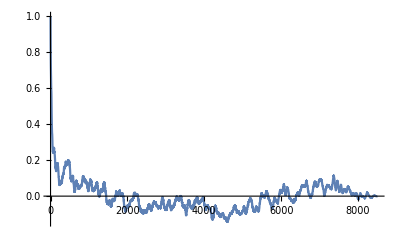

```mathematica
ListLinePlot[corr20,PlotRange->All]
```

```mathematica
corr=Table[{i/6,CorrelationFunction[Vel20ok[[All,2]],i]},{i,0,Length[Vel20ok]-1,1}]
```

{{0,1.},{1/6,0.974517},{1/3,0.958902},{1/2,0.947825},{2/3,0.938612},{5/6,0.929781},51025,{51031/6,-0.0000613427},{25516/3,-0.0000497155},{17011/2,-0.0000391691},{25517/3,-0.0000234532},{51035/6,-0.0000114864}}
 |  |  |  |

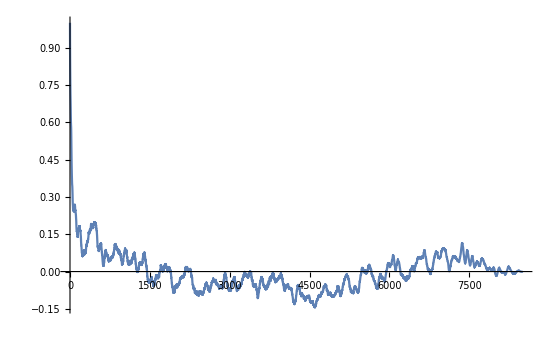

```mathematica
ListLinePlot[corr,PlotRange->All]
```

```mathematica
FirstPosition[corr[[All,2]],x_/;x<0]
```

{7592}

```mathematica
N[corr[[7592]]]
```

{1265.17,-0.000153285}

```mathematica
corrfunc=Interpolation[corr[[1;;7592]],x]
```

InterpolatingFunction[…][x]

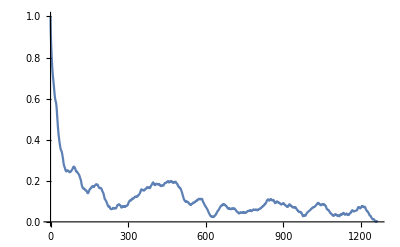

```mathematica
Plot[corrfunc,{x,0,1265.17},PlotRange->All]
```

```mathematica
IntTime=Integrate[corrfunc,{x,0,1265.17}]
```

InterpolatingFunction::dmvali: The integration endpoint 1265.17 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

148.396

```mathematica
IntLong=IntTime μ20
```

755.161

```mathematica
PSDWSpeed[data_]:=Module[{Δt,Npts,xf,PSD,res},Δt=data[[2,1]]-data[[1,1]];Npts=Length[data];xf=Table[N[i],{i,0,1/(2Δt),(1/(2Δt))/((Npts/2)-1)}];PSD=Δt Abs[Fourier[data[[All,2]]]]^2;res=Transpose[Join[{xf},{ xf PSD[[1;;Npts/2]]}]];res]
```

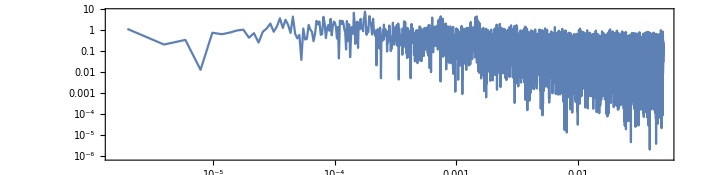

```mathematica
ListLogLogPlot[PSDWSpeed[Vel20ok],PlotRange->All,Joined->True,AspectRatio->0.25,Frame->True]
```